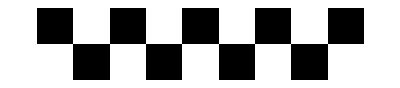

```mathematica
ArrayPlot[{{1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0}}]
```

```mathematica
NumToRegla[num_]:=Module[{lista,numlist,i,base},
lista = {};
numlist = Reverse[IntegerDigits[num,2,8]];
For[i=1,i≤Length[numlist],i++,
base = Reverse[IntegerDigits[i-1,2,3]];
AppendTo[lista,AppendTo[base,numlist[[i]]]];
];
Return[lista];
];
```

```mathematica
NumToRegla[54]
```

{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0},{1,1,1,0}}

```mathematica
NextConfig[estado_,regla_]:=Module[{lenestado,i,triplete,sol,result},
lenestado = Length[estado];
sol = {};
For[i=1,i≤lenestado,i++,
If[i==1,
triplete = {estado[[lenestado]],estado[[i]],estado[[i+1]],_};
,
If[i==lenestado,
triplete = {estado[[i-1]],estado[[i]],estado[[1]],_};
,
triplete = {estado[[i-1]],estado[[i]],estado[[i+1]],_};
];
];
result = Cases[regla,triplete];
AppendTo[sol,result[[1]][[4]]];
];
Return[sol];
];
```

```mathematica
NextConfig[{1,0,1,0,0,0,1,0},{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0},{1,1,1,0}}]
```

{1,1,1,1,0,1,1,1}

```mathematica
Simulacion[inicial_,regla_,t_]:=Module[{reglalist,i,print,estado},
reglalist= NumToRegla[regla];
print = {};
estado=inicial;
AppendTo[print,inicial];
For[i=1,i≤t,i++,
estado = NextConfig[estado,reglalist];
AppendTo[print,estado];
];
Return[ArrayPlot[print]];
];
```

```mathematica
SimulacionAnimate[{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},77,22
]
```

```mathematica
SimulacionAnimate[inicial_,regla_,t_]:=Module[{reglalist,i,print,estado,leninicial,sample, j,frame},
reglalist= NumToRegla[regla];
print = {};
estado=inicial;
leninicial = Length[inicial];
sample = {};
frame = {};
For[j=1,j≤leninicial,j++,
AppendTo[sample,0];
];
For[j=1,j≤leninicial,j++,
AppendTo[frame,sample];
];
AppendTo[print, ArrayPlot[frame]];
For[i=1,i≤t,i++,
frame = Rest[frame];
AppendTo[frame,estado];
estado = NextConfig[estado,reglalist];
AppendTo[print, ArrayPlot[frame]];
];
Return[ListAnimate[print]];
];
```

practica 2

```mathematica
sampleAutomata = {{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{q},{r}}
```

{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{q},{r}}

```mathematica
AfdToAc[automata_]:=Module[{states,symbols,transitions,rules,i,j,final},
states=automata[[1]];
symbols = automata[[2]];
transitions =automata[[3]];
final = automata[[5]];
rules = {};
For[i=1,i≤Length[states],i++,
For[j=1,j≤Length[states],j++,
AppendTo[rules,{states[[i]],states[[j]],states[[j]]}];
];
];
For[i=1,i≤Length[symbols],i++,
For[j=1,j≤Length[symbols],j++,
AppendTo[rules,{symbols[[i]],symbols[[j]],symbols[[j]]}];
];
];
For[i=1,i≤Length[transitions],i++,
AppendTo[rules,transitions[[i]]];
];
Return[{Union[states],Union[rules],Union[final]}];
];
```

```mathematica
sampleCelular = AfdToAc[sampleAutomata]
```

{{p,q,r},{{a,a,a},{a,b,b},{b,a,a},{b,b,b},{p,a,r},{p,b,q},{p,p,p},{p,q,q},{p,r,r},{q,a,p},{q,b,r},{q,p,p},{q,q,q},{q,r,r},{r,a,r},{r,b,r},{r,p,p},{r,q,q},{r,r,r}},{r}}

```mathematica
NextConfigOneWay[estado_,regla_]:=Module[{lenestado,i,doblete,sol,result},
lenestado = Length[estado];
sol = {};
For[i=2,i≤lenestado,i++,
doblete= {estado[[i-1]],estado[[i]],_};
result = Cases[regla,doblete];
AppendTo[sol,result[[1]][[3]]];
];
sol=Prepend[sol,estado[[1]]];
Return[sol];
];
```

```mathematica
ReconoceRPOCA[ac_,palabra_,q_]:=Module[{s,rules,splus,n,word,i},
s=ac[[1]];
rules = ac[[2]];
splus = ac[[3]];
n = Length[palabra];
word = Prepend[palabra,q];
For[i=1,i≤n,i++,
word = NextConfigOneWay[word,rules];
];
Return [MemberQ[splus,word[[n+1]]]];
];
```

```mathematica
ReconoceRPOCA[sampleCelular,{a,b,a,a,b},q]
```

True

```mathematica
RPOCAPlot [ac_,palabra_,q_]:=Module[{s,rules,splus,n,word,i,print,items,colors,colorpattern},
s=ac[[1]];
rules = ac[[2]];
splus = ac[[3]];
n = Length[palabra];
word = Prepend[palabra,q];
print ={};
PrependTo[print,Rest[word]];
For[i=1,i≤n,i++,
word = NextConfigOneWay[word,rules];
PrependTo[print,Rest[word]];
];
items=Union[Flatten[rules]];
colors=ColorList[Length[items]];
colorpattern = {};
For[i=1,i≤Length[items],i++,
AppendTo[colorpattern,items[[i]]->colors[[i]]];
];
Return [ArrayPlot[print,ColorRules->colorpattern]];
];
```

```mathematica
ColorList[numb_]:=Module[{sol,i,j,k,increase,parts},
parts =Floor[CubeRoot[numb-1]];
increase = 1/parts;
sol={};
For[i=0,i≤1,i=i+increase,
For[j=0,j≤1,j=j+increase,
For[k=0,k≤1,k=k+increase,
AppendTo[sol,{RGBColor[i,j,k]}];
];
];
];
Return[RandomSample[sol]];
];
```

```mathematica
ColorList[28]
```

{{RGBColor[Rational[2, 3], 0, Rational[2, 3]]},{RGBColor[1, Rational[1, 3], 1]},{RGBColor[Rational[2, 3], 0, 0]},{RGBColor[1, Rational[2, 3], Rational[2, 3]]},{RGBColor[0, Rational[1, 3], Rational[2, 3]]},{RGBColor[0, 0, 0]},{RGBColor[0, 0, Rational[1, 3]]},{RGBColor[Rational[1, 3], 0, 1]},{RGBColor[1, Rational[2, 3], 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], 1]},{RGBColor[0, 1, 1]},{RGBColor[1, 1, 1]},{RGBColor[Rational[2, 3], Rational[2, 3], 1]},{RGBColor[Rational[1, 3], 1, 1]},{RGBColor[1, 0, Rational[1, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], Rational[2, 3]]},{RGBColor[0, Rational[2, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[1, 3], 1]},{RGBColor[Rational[1, 3], 0, 0]},{RGBColor[Rational[1, 3], 0, Rational[1, 3]]},{RGBColor[1, 1, 0]},{RGBColor[Rational[1, 3], Rational[2, 3], Rational[1, 3]]},{RGBColor[0, Rational[2, 3], 0]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]},{RGBColor[1, Rational[1, 3], 0]},{RGBColor[Rational[2, 3], Rational[1, 3], Rational[2, 3]]},{RGBColor[0, Rational[2, 3], 1]},{RGBColor[Rational[2, 3], Rational[2, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], 1, Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], 0]},{RGBColor[Rational[2, 3], 0, Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[1, 3], 1]},{RGBColor[1, 0, 1]},{RGBColor[1, Rational[1, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[1, 3], 0]},{RGBColor[Rational[1, 3], Rational[1, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[1, 3], Rational[1, 3]]},{RGBColor[1, Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[2, 3], 1, 1]},{RGBColor[Rational[2, 3], 1, 0]},{RGBColor[Rational[2, 3], Rational[1, 3], Rational[1, 3]]},{RGBColor[Rational[1, 3], 1, Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[2, 3], 0]},{RGBColor[Rational[2, 3], 1, Rational[1, 3]]},{RGBColor[0, Rational[1, 3], Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[1, 3], 0]},{RGBColor[0, Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[1, 3], 0, Rational[2, 3]]},{RGBColor[0, 1, Rational[2, 3]]},{RGBColor[Rational[2, 3], 0, 1]},{RGBColor[0, Rational[1, 3], 0]},{RGBColor[1, 0, 0]},{RGBColor[Rational[2, 3], 1, Rational[2, 3]]},{RGBColor[0, 1, Rational[1, 3]]},{RGBColor[1, 0, Rational[2, 3]]},{RGBColor[1, 1, Rational[1, 3]]},{RGBColor[1, Rational[2, 3], 1]},{RGBColor[0, 0, 1]},{RGBColor[0, Rational[1, 3], 1]},{RGBColor[1, 1, Rational[2, 3]]},{RGBColor[Rational[1, 3], 1, 0]}}

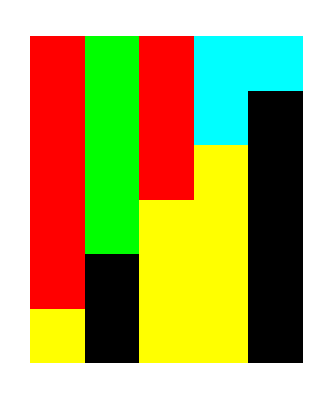

```mathematica
RPOCAPlot[sampleCelular,{a,b,a,a,b},q]
```